```mathematica
λ=630.0;
f=93.2*1.123;
```

```mathematica
NULL = ConstantArray[0,{10,10}];
```

```mathematica
SP=DiagonalMatrix[{-1.84,-1.84,-1.83,-2.0,-2.25,-2.38,-2.0,-2.0,-2.67,-2.67}];
```

```mathematica
MM=DiagonalMatrix[{493.677,497.672,134.9764,134.9764,547.45,547.45,139.56995,139.56995,493.677,497.672}];
```

```mathematica
BM=DiagonalMatrix[{938.27231,939.56563,1115.684,1192.55,1115.684,1192.55,1197.436,1189.37,1321.32,1314.9}];
```

```mathematica
CC=({{2, 1, (√3)/2, 0.5, 1.5, (√3)/2, 0, 1.0, 0, 0}, {1, 2, -(√3)/2, 0.5, 1.5, -(√3)/2, 1, 0, 0, 0}, {(√3)/2, -(√3)/2, 0, 0, 0, 0, 0, 0, (√3)/2, -(√3)/2}, {0.5, 0.5, 0, 0, 0, 0, 2, 2, 0.5, 0.5}, {1.5, 1.5, 0, 0, 0, 0, 0, 0, 1.5, 1.5}, {(√3)/2, -(√3)/2, 0, 0, 0, 0, 0, 0, (√3)/2, -(√3)/2}, {0, 1, 0, 2, 0, 0, 2, 0, 2, 0}, {1, 0, 0, 2, 0, 0, 0, 2, 0, 1}, {0, 0, (√3)/2, 0.5, 1.5, (√3)/2, 2, 0, 2, 1}, {0, 0, -(√3)/2, 0.5, 1.5, -(√3)/2, 0, 1, 1, 2}})
```

{{2,1,(√3)/2,0.5,1.5,(√3)/2,0,1.,0,0},{1,2,-(√3)/2,0.5,1.5,-(√3)/2,1,0,0,0},{(√3)/2,-(√3)/2,0,0,0,0,0,0,(√3)/2,-(√3)/2},{0.5,0.5,0,0,0,0,2,2,0.5,0.5},{1.5,1.5,0,0,0,0,0,0,1.5,1.5},{(√3)/2,-(√3)/2,0,0,0,0,0,0,(√3)/2,-(√3)/2},{0,1,0,2,0,0,2,0,2,0},{1,0,0,2,0,0,0,2,0,1},{0,0,(√3)/2,0.5,1.5,(√3)/2,2,0,2,1},{0,0,-(√3)/2,0.5,1.5,-(√3)/2,0,1,1,2}}

```mathematica
ID = NULL;
```

```mathematica
Do[ID[[a,a]] = 1.0,{a,1,10,1}]
ID//MatrixForm;
```

```mathematica
V=NULL;
Do[Do[V[[a,b]] = (-CC[[a,b]])/(4 f^2)(2Ecm - BM[[a,a]]-BM[[b,b]]),{a,1,10,1}],{b,1,10,1}]
V//MatrixForm
```

(-0.0000456435 (-1876.54+2 Ecm) | -0.0000228217 (-1877.84+2 Ecm) | -0.0000197642 (-2053.96+2 Ecm) | -0.0000114109 (-2130.82+2 Ecm) | -0.0000342326 (-2053.96+2 Ecm) | -0.0000197642 (-2130.82+2 Ecm) | 0. | -0.0000228217 (-2127.64+2 Ecm) | 0. | 0.
-0.0000228217 (-1877.84+2 Ecm) | -0.0000456435 (-1879.13+2 Ecm) | 0.0000197642 (-2055.25+2 Ecm) | -0.0000114109 (-2132.12+2 Ecm) | -0.0000342326 (-2055.25+2 Ecm) | 0.0000197642 (-2132.12+2 Ecm) | -0.0000228217 (-2137.+2 Ecm) | 0. | 0. | 0.
-0.0000197642 (-2053.96+2 Ecm) | 0.0000197642 (-2055.25+2 Ecm) | 0. | 0. | 0. | 0. | 0. | 0. | -0.0000197642 (-2437.+2 Ecm) | 0.0000197642 (-2430.58+2 Ecm)
-0.0000114109 (-2130.82+2 Ecm) | -0.0000114109 (-2132.12+2 Ecm) | 0. | 0. | 0. | 0. | -0.0000456435 (-2389.99+2 Ecm) | -0.0000456435 (-2381.92+2 Ecm) | -0.0000114109 (-2513.87+2 Ecm) | -0.0000114109 (-2507.45+2 Ecm)
-0.0000342326 (-2053.96+2 Ecm) | -0.0000342326 (-2055.25+2 Ecm) | 0. | 0. | 0. | 0. | 0. | 0. | -0.0000342326 (-2437.+2 Ecm) | -0.0000342326 (-2430.58+2 Ecm)
-0.0000197642 (-2130.82+2 Ecm) | 0.0000197642 (-2132.12+2 Ecm) | 0. | 0. | 0. | 0. | 0. | 0. | -0.0000197642 (-2513.87+2 Ecm) | 0.0000197642 (-2507.45+2 Ecm)
0. | -0.0000228217 (-2137.+2 Ecm) | 0. | -0.0000456435 (-2389.99+2 Ecm) | 0. | 0. | -0.0000456435 (-2394.87+2 Ecm) | 0. | -0.0000456435 (-2518.76+2 Ecm) | 0.
-0.0000228217 (-2127.64+2 Ecm) | 0. | 0. | -0.0000456435 (-2381.92+2 Ecm) | 0. | 0. | 0. | -0.0000456435 (-2378.74+2 Ecm) | 0. | -0.0000228217 (-2504.27+2 Ecm)
0. | 0. | -0.0000197642 (-2437.+2 Ecm) | -0.0000114109 (-2513.87+2 Ecm) | -0.0000342326 (-2437.+2 Ecm) | -0.0000197642 (-2513.87+2 Ecm) | -0.0000456435 (-2518.76+2 Ecm) | 0. | -0.0000456435 (-2642.64+2 Ecm) | -0.0000228217 (-2636.22+2 Ecm)
0. | 0. | 0.0000197642 (-2430.58+2 Ecm) | -0.0000114109 (-2507.45+2 Ecm) | -0.0000342326 (-2430.58+2 Ecm) | 0.0000197642 (-2507.45+2 Ecm) | 0. | -0.0000228217 (-2504.27+2 Ecm) | -0.0000228217 (-2636.22+2 Ecm) | -0.0000456435 (-2629.8+2 Ecm))

```mathematica
XI = NULL;
Do[XI[[a,a]] =√((Ecm^2 - (MM[[a,a]]-BM[[a,a]])^2)(Ecm^2-(MM[[a,a]]+BM[[a,a]])^2)),{a,1,10,1}];
XI//MatrixForm
```

(√((-2.05048×10^6+Ecm^2) (-197665.+Ecm^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √((-2.06565×10^6+Ecm^2) (-195270.+Ecm^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √((-1.56415×10^6+Ecm^2) (-961787.+Ecm^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | √((-1.76233×10^6+Ecm^2) (-1.11846×10^6+Ecm^2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | √((-2.76601×10^6+Ecm^2) (-322890.+Ecm^2)) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | √((-3.0276×10^6+Ecm^2) (-416154.+Ecm^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √((-1.78758×10^6+Ecm^2) (-1.11908×10^6+Ecm^2)) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | √((-1.76608×10^6+Ecm^2) (-1.10208×10^6+Ecm^2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √((-3.29421×10^6+Ecm^2) (-684993.+Ecm^2)) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √((-3.28542×10^6+Ecm^2) (-667862.+Ecm^2)))

```mathematica
GF= NULL;
Do[GF[[a,a]]=(2 BM[[a,a]])/(4 π)^2(SP[[a,a]]+(MM[[a,a]]^2-BM[[a,a]]^2+Ecm^2)/(2 Ecm^2)Log[MM[[a,a]]^2/BM[[a,a]]^2]+XI[[a,a]]/(2 Ecm^2)(Log[(Ecm^2-(BM[[a,a]]^2-MM[[a,a]]^2)+XI[[a,a]])]+Log[(Ecm^2+(BM[[a,a]]^2-MM[[a,a]]^2)+XI[[a,a]])]-Log[(-Ecm^2+(BM[[a,a]]^2-MM[[a,a]]^2)+XI[[a,a]])]-Log[(-Ecm^2-(BM[[a,a]]^2-MM[[a,a]]^2)+XI[[a,a]])])+Log[BM[[a,a]]^2/λ^2]),{a,1,10,1}];
GF;
```

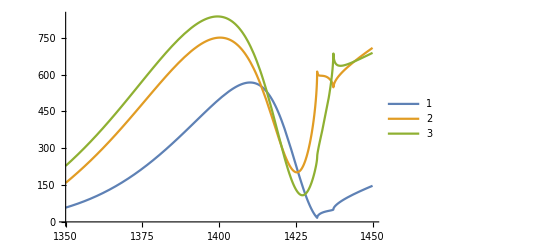

```mathematica
CH1 = 1;
CH2 = 1;
Plot[{XI[[4,4]] Abs[(Inverse[ID-V.GF].V)[[4,4]]]^2,XI[[7,7]] Abs[(Inverse[ID-V.GF].V)[[7,7]]]^2,XI[[8,8]] Abs[(Inverse[ID-V.GF].V)[[8,8]]]^2},{Ecm,1350,1450},PlotLegends->{"1","2","3"}]
```